## 1

```mathematica
Orthogonal[S_,ip_]:=Module[{l,Sot},
l=Dimensions[S][[1]];
Sot[1]=S[[1]];
For[i=2,i<=l,i++,
Sot[i]=S⟦i⟧-Sum[ip[S⟦i⟧,Sot[j]]/ip[Sot[j],Sot[j]] Sot[j],{j,1,i-1}]];
Table[Sot[i],{i,1,l}]]
```

```mathematica
Orthonomal[Sot_,ip_]:=Module[{l,Son},
l=Dimensions[Sot][[1]];
Son=Table[0,l,l];
For[i=1,i<=l,i++,
Son[[i]]=Sot[[i]]/Sqrt[ip[Sot[[i]],Sot[[i]]]]];
Son]
```

## 2.

```mathematica
S={{4,5,3},{4,5,-1},{1,2,9}};
```

```mathematica
ip[a_,b_]:=a.b
```

```mathematica
Sot=Orthogonal[S,ip];
Son=Orthonomal[Sot,ip];
```

```mathematica
Table[ip[Sot[[i]],Sot[[j]]],{i,1,Dimensions[Sot][[1]]},{j,1,Dimensions[Sot][[1]]}]//MatrixForm
```

(50 | 0 | 0
0 | 328/25 | 0
0 | 0 | 9/41)

```mathematica
Table[ip[Son[[i]],Son[[j]]],{i,1,Dimensions[Son][[1]]},{j,1,Dimensions[Son][[1]]}]//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

## 3.

```mathematica
Clear[S,ip,Sot,Son]
```

#### 3.a

```mathematica
p=10;
S=Table[x^(i-1),{i,1,p+1}];
```

```mathematica
scale[S_]:=Table[S[[i]]/(S[[i]]/.x->1),{i,Length[S]}]
```

```mathematica
ip[a_,b_]:=Integrate[a b,{x,-1,1}]
```

#### 3.b

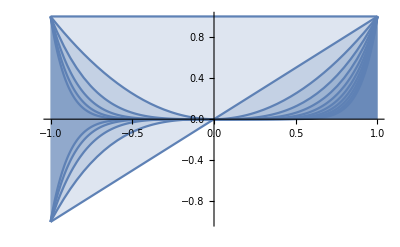

```mathematica
Plot[Table[S[[i]],{i,1,Length[S]}],{x,-1,1},Filling->Axis]
```

```mathematica
Sot=Orthogonal[S,ip];
Son=Orthonomal[Sot,ip];
```

```mathematica
Table[ip[Sot[[i]],Sot[[j]]],{i,1,Dimensions[Sot][[1]]},{j,1,Dimensions[Sot][[1]]}]//MatrixForm
```

(2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 8/45 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 8/175 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 128/11025 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 128/43659 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 512/693693 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 512/2760615 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 32768/703956825 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 32768/2807136475 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 131072/44801898141)

```mathematica
Sos=scale[Sot];
```

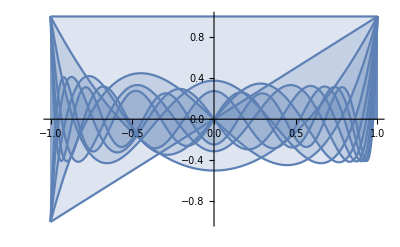

```mathematica
Plot[Table[Sos[[i]],{i,1,Length[Sot]}],{x,-1,1},Filling->Axis]
```

#### 3.c

```mathematica
Table[LegendreP[i,x]-Sos[[i+1]],{i,1,Length[Sos]-1}]//Simplify
```

{0,0,0,0,0,0,0,0,0,0}

#### 3.d

```mathematica
Table[y=LegendreP[n-1,x];
(1-x^2)D[y,{x,2}]-2x D[y,x]+n (n-1) y,{n,0,10}]//Simplify
```

{0,0,0,0,0,0,0,0,0,0,0}

## 4.

```mathematica
Clear[ip,Sot]
```

#### 4.a

```mathematica
ip[a_,b_]:=Integrate[a b/Sqrt[1-x^2],{x,-1,1}]
```

```mathematica
Sot=Orthogonal[S,ip];
```

```mathematica
Table[ip[Sot[[i]],Sot[[j]]],{i,1,Dimensions[Sot][[1]]},{j,1,Dimensions[Sot][[1]]}]//MatrixForm
```

(π | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | π/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | π/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | π/32 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | π/128 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | π/512 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | π/2048 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | π/8192 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | π/32768 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | π/131072 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | π/524288)

#### 4.b

```mathematica
Sos=scale[Sot];
```

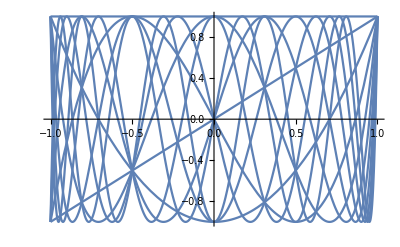

```mathematica
Plot[Table[Sos[[i]],{i,1,Length[Sot]}],{x,-1,1}]
```

#### 4.c

```mathematica
Table[LegendreP[i,x]-Sos[[i+1]],{i,1,Length[Sos]-1}]//Simplify
```

{0,1/2 (1-x^2),-3/2 x (-1+x^2),1/8 (-5+34 x^2-29 x^4),-5/8 x (5-18 x^2+13 x^4),1/16 (11-183 x^2+453 x^4-281 x^6),-7/16 x (-11+83 x^2-157 x^4+85 x^6),1/128 (-93+2836 x^2-13550 x^4+20756 x^6-9949 x^8),-3/128 x (279-3580 x^2+12426 x^4-15996 x^6+6871 x^8),1/256 (193-9335 x^2+72370 x^4-196630 x^6+218285 x^8-84883 x^10)}